```mathematica
ClearAll["Global`*"]
```

```mathematica
ℏ=1.0*10^-34;
kb=1.38*10^-23;
T0=6.4*10^-6;
m171=170.936*(1.660539*10^-27);
```

```mathematica
ωt=2π* 67.*10.^3;
```

```mathematica
Pn[n_,T_]:=E^(-ℏ ωt n/(kb T))(1-E^(-ℏ ωt/(kb T)))
T[nbar_]:=(ℏ ωt)/(kb Log[1/nbar+1])
```

## H form

```mathematica
n0=11;
a=DiagonalMatrix[Table[√(n0-n),{n,0,n0}]];
MatrixForm[a];
For[i=n0,i>0n0,i--,
a[[{i,i+1}]]=a[[{i+1,i}]];
]
MatrixForm[a];
MatrixForm[a†];
σ=({{0, 0}, {1, 0}});
```

```mathematica
Hr=KroneckerProduct[Ω/2(IdentityMatrix[n0+1]+Sum[(I η)^n/(n!) MatrixPower[a+a†,n],{n,1,n0}]),σ†];
HR=Hr+Hr†;
MatrixForm[Hr];
MatrixForm[HR];
```

```mathematica
Hs0=({{-1/2 δ, 0}, {0, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ω, 0}, {0, ω}})];
H=Hs+Hm+HR;
MatrixForm[H];
```

```mathematica
nbar=1.5;
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
ωt=2π 60.*10^3;
Ωr=2π 2*10^4;
Ttot=10*(2π)/Ωr;
k=√2(2π)/(556.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
Pns[[n0]]=1-Sum[Pns[[n]],{n,1,n0-1}]
```

0.00604662

```mathematica
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
NMaximize[{ρi[t],{t>0.,t<Ttot}},t]
```

{0.879215,{t→0.0000285573}}

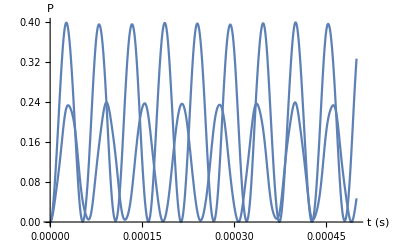

```mathematica
Plot[Table[Evaluate[ρ[t]/.ρs][[1,n,n]],{n,2*n0-1,2*n0+1,2}],{t,0,Ttot},PlotRange->All,PlotLegends->{},AxesLabel->{"t (s)","P"}]
```

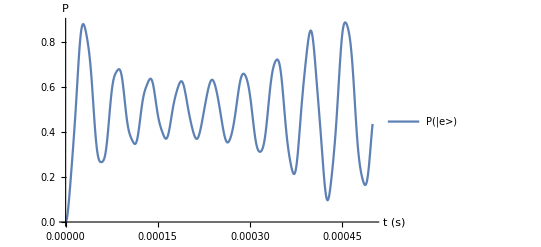

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*n0+1,2}],{t,0,Ttot},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"}]
```

### get the pi pulse fidelity for a given Ωr and ωt

```mathematica
Ωr=2π 2.*10^4;
Ttot=(2π)/Ωr;
k=√2(2π)/(556.*10^-9);
```

```mathematica
ωt=2π 67*10.^3;
E0=1/2 ℏ ωt;
v0=√((2E0)/m171);
fdopp=1/(2π)v0*k
```

30976.1

#### vary trap freq

```mathematica
nbars=Table[i*0.2,{i,1,5}];
numGrid=50;
ωts=2π Subdivide[2.*10^3,2.*10^5,numGrid-1];
piFidelities=Table[{ωts[[i]]/(2π)*10^-3,0},{j,1,Length[nbars]},{i,1,numGrid}];
```

```mathematica
For[jj=1,jj≤Length[nbars],jj++,
For[ii=1,ii≤numGrid,ii++,
ωt =ωts[[ii]];
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
piFidelities[[jj,ii,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
Print[jj]
]
```

1

2

3

4

5

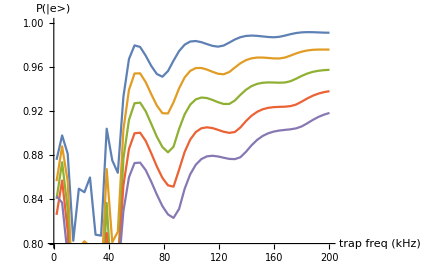

```mathematica
ListPlot[{piFidelities[[1]],piFidelities[[2]],piFidelities[[3]],piFidelities[[4]],piFidelities[[5]]},Joined->True,PlotRange->{0.8,1.0},AxesLabel->{"trap freq (kHz)", "P(|e>)"}]
```

#### vary temp

```mathematica
numTs=100;
nbars=Table[i*0.05,{i,1,numTs}];
ωt=2π 67.*10^3;
piFidelities=Table[{nbars[[i]],0},{i,1,Length[nbars]}];
```

```mathematica
For[jj=1,jj≤Length[nbars],jj++,
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
```

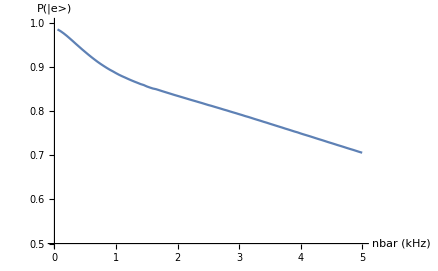

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.5,1.0},AxesLabel->{"nbar (kHz)", "P(|e>)"}]
```

#### raman rabi freq

```mathematica
numTs=30;
nbar=0.1;
ωt=2π 67.*10^3;
Ωrs=Table[2π *i*20.*10^3,{i,1,numTs}];
piFidelities=Table[{Ωrs[[i]]*10^-3/(2π),0},{i,1,Length[Ωrs]}];
```

```mathematica
For[jj=1,jj≤Length[Ωrs],jj++,
ωR=(ℏ k^2)/(2 m171);
Ωr=Ωrs[[jj]];
Ttot=(2π)/Ωr;
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
```

$Aborted

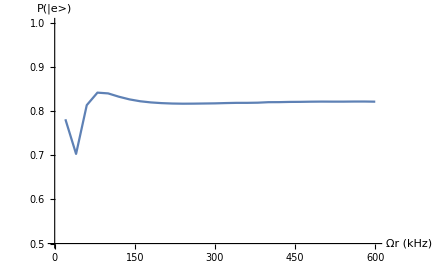

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.5,1.0},AxesLabel->{"Ωr (kHz)", "P(|e>)"}]
```

## no η expansion

```mathematica
n0=6;
a=DiagonalMatrix[Table[√(n0-n),{n,0,n0}]];
For[i=n0,i>0n0,i--,
a[[{i,i+1}]]=a[[{i+1,i}]];
]
σ=({{0, 0}, {1, 0}});
```

```mathematica
Hr=KroneckerProduct[Ω/2 MatrixExp[I η (a+a†)],σ†];
HR=Hr+Hr†;
MatrixForm[HR];
```

```mathematica
Hs0=({{-1/2 δ, 0}, {0, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ω, 0}, {0, ω}})];
H=Hs+Hm+HR;
MatrixForm[H];
```

```mathematica
nbar=0.3;
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
ωt=2π 64.*10^3;
Ωr=2π 1.7*10^4;
Ttot=5*(2π)/Ωr;
k=√2(2π)/(556.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
Pns[[n0]]=1-Sum[Pns[[n]],{n,1,n0-1}]
```

0.00065447

```mathematica
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
NMaximize[{ρi[t],{t>0.,t<Ttot}},t]
```

{0.978632,{t→0.0000267981}}

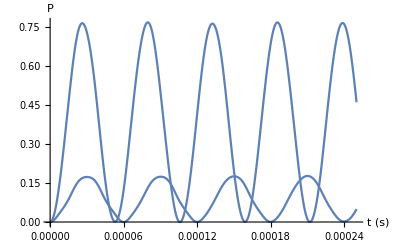

```mathematica
Plot[Table[Evaluate[ρ[t]/.ρs][[1,n,n]],{n,2*n0-1,2*n0+1,2}],{t,0,Ttot},PlotRange->All,PlotLegends->{},AxesLabel->{"t (s)","P"}]
```

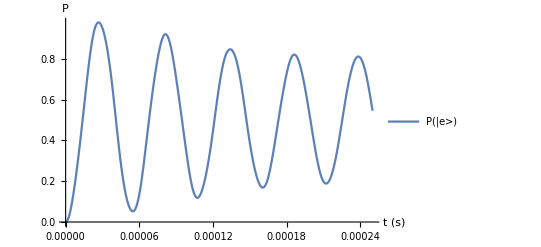

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*n0+1,2}],{t,0,Ttot},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"}]
```

#### raman rabi freq

```mathematica
numTs=50;
nbar=0.1;
ωt=2π 40.*10^3;
Ωrs=Table[2π *i*1.*10^3,{i,1,numTs}];
piFidelities=Table[{Ωrs[[i]]*10^-3/(2π),0},{i,1,Length[Ωrs]}];
```

```mathematica
For[jj=1,jj≤Length[Ωrs],jj++,
ωR=(ℏ k^2)/(2 m171);
Ωr=Ωrs[[jj]];
Ttot=(1.5π)/Ωr;
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(40 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
If[Mod[jj,5]==0,Print[jj]]
];
```

5

10

15

20

25

30

35

40

45

50

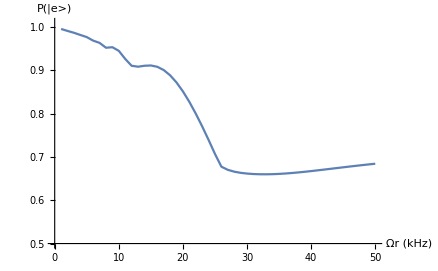

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.5,1.01},AxesLabel->{"Ωr (kHz)", "P(|e>)"}]
```

```mathematica
η0
```

0.326916

## 3 level

```mathematica
Clear["Global`*"]
```

```mathematica
Hs0=({{0, Ω1/2, Ω2/2}, {Ω1/2, δ1, 0}, {Ω2/2, 0, δ2}});
```

```mathematica
Ωr=2π 130.*10^3;
Δ=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ));
Ω20=√(Ωr*(2*Δ));
Ttot=1(2π)/Ωr;
```

```mathematica
Hn=Hs0/.{Ω2->Ω20,Ω1->Ω10,δ1->-Δ,δ2->-Δ};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->7];
```

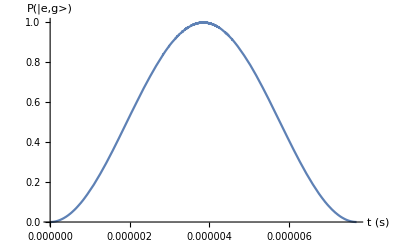

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|e,g>)"}]
```

## 4 level counter rotating

```mathematica
Clear[Δ]
```

```mathematica
Ha0=({{0, 0, 0, 0}, {0, Δe, 0, 0}, {0, 0, -ω0+Δqb, 0}, {0, 0, 0, -ω0}});
Haf0=1/2({{0, 0, Ω2 E^(I(ω0-Δ) t), Ω1 E^(I (ω0-Δ-Δqb+df) t)}, {0, 0, Ω1 E^(I (ω0-Δ-Δqb+df) t), Ω2 E^(I (ω0-Δ) t)}, {Ω2 E^(-I (ω0-Δ) t), Ω1 E^(-I (ω0-Δ-Δqb+df) t), 0, 0}, {Ω1 E^(-I (ω0-Δ-Δqb+df) t), Ω2 E^(-I (ω0-Δ) t), 0, 0}});
U=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, E^(I (ω0-Δ-Δqb+df) t), 0}, {0, 0, 0, E^(I (ω0-Δ) t)}});
Ha=U.Ha0.U†;
MatrixForm[Ha];
Haf=U.Haf0.U†;
H=Ha+Haf-I D[U,t].U†;
FullSimplify[MatrixForm[H],Assumptions->{ω0∈Reals,t∈Reals,,Δ∈Reals,df∈Reals,Δqb∈Reals}]
```

(0 | 0 | 1/2 ⅇ^(ⅈ t (-df+Δqb)) Ω2 | 1/2 ⅇ^(ⅈ t (df-Δqb)) Ω1
0 | Δe | Ω1/2 | Ω2/2
1/2 ⅇ^(ⅈ t (df-Δqb)) Ω2 | Ω1/2 | df-Δ | 0
1/2 ⅇ^(-ⅈ t (df-Δqb)) Ω1 | Ω2/2 | 0 | -Δ)

```mathematica
Hs=({{0, 0, 1/2 ⅇ^(ⅈ t (-df+Δqb)) Ω2, 1/2 ⅇ^(ⅈ t (df-Δqb)) Ω1}, {0, Δe, Ω1/2, Ω2/2}, {1/2 ⅇ^(ⅈ t (df-Δqb)) Ω2, Ω1/2, df-Δ, 0}, {1/2 ⅇ^(-ⅈ t (df-Δqb)) Ω1, Ω2/2, 0, -Δ}});
```

```mathematica
Ωr=2π 180.*10^3;
Δ0=2π 240.*10^6;
Ω10=1.2 √(Ωr*(2*Δ0));
Ω20=0.8 √(Ωr*(2*Δ0));
Ttot=(2π)/Ωr;
Δqb0=2π 50.*10^3;
```

```mathematica
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->Δqb0,Δe->-2π 20.*10^6,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->7];
```

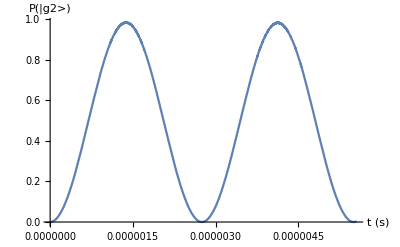

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,3]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"}]
```

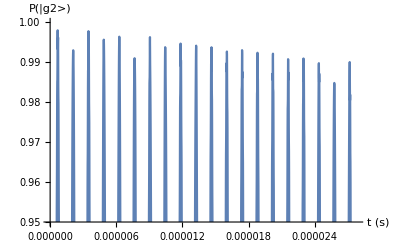

```mathematica
Ωr=2π 180.*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=5(2π)/Ωr;
Δqb0=2π 16.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->Δqb0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->7];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0.95,1}]
```

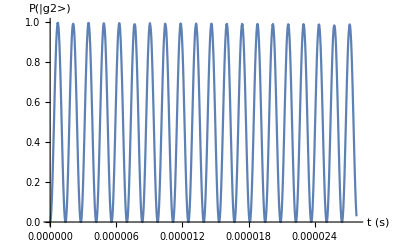

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

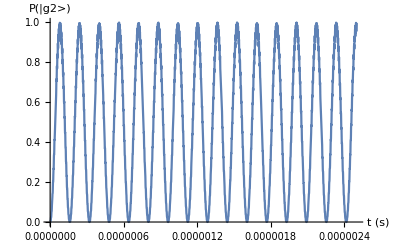

```mathematica
Ωr=2π 1600.*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=4(2π)/Ωr;
Δqb0=2π 16.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

```mathematica
Ωr=2π 180./4*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=4(2π)/Ωr;
Δqb0=2π 16.*10^3;
```

```mathematica
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->7];
```

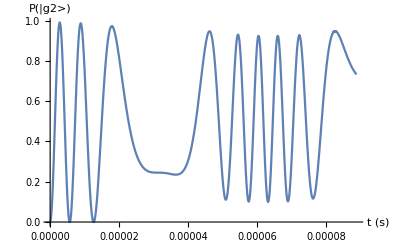

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"}]
```

```mathematica
Ωr=2π 16*10^3;
Δ0=2π 240.*10^6;
Ω10=1.2*√(Ωr*(2*Δ0));
Ω20=0.8*√(Ωr*(2*Δ0));
Ttot=4(2π)/Ωr;
Δqb0=2π 16.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->Δqb0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

Dot::dotsh: Tensors {{0,0,6.96499×10^6+0. ⅈ,1.04475×10^7+0. ⅈ},{0,Δe,1.04475×10^7,6.96499×10^6},{6.96499×10^6+0. ⅈ,1.04475×10^7,-1.50786×10^9,0},{1.04475×10^7+0. ⅈ,6.96499×10^6,0,-1.50796×10^9}} and {0.,0.,1.} have incompatible shapes.

Dot::dotsh: Tensors {{0.,0.,6.96499×10^6+0. ⅈ,1.04475×10^7+0. ⅈ},{0.,Δe,1.04475×10^7,6.96499×10^6},{6.96499×10^6+0. ⅈ,1.04475×10^7,-1.50786×10^9,0.},{1.04475×10^7+0. ⅈ,6.96499×10^6,0.,-1.50796×10^9}} and {0.,0.,1.} have incompatible shapes.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{ⅈ ψ'[5.10714×10^-9]=={{0,0,6.96499×10^6+0. ⅈ,1.04475×10^7+0. ⅈ},{0,Δe,1.04475×10^7,6.96499×10^6},{6.96499×10^6+0. ⅈ,1.04475×10^7,-1.50786×10^9,0},{1.04475×10^7+0. ⅈ,6.96499×10^6,0,-1.50796×10^9}}.ψ[5.10714×10^-9],ψ[0]=={0,0,1}},ψ,{5.10714×10^-9,0,1/4000},AccuracyGoal→9]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 5.10714×10^-9 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{ⅈ ψ'[5.10714×10^-9]=={{0,0,6.96499×10^6+0. ⅈ,1.04475×10^7+0. ⅈ},{0,Δe,1.04475×10^7,6.96499×10^6},{6.96499×10^6+0. ⅈ,1.04475×10^7,-1.50786×10^9,0},{1.04475×10^7+0. ⅈ,6.96499×10^6,0,-1.50796×10^9}}.ψ[5.10714×10^-9],ψ[0]=={0,0,1}},ψ,{5.10714×10^-9,0,1/4000},AccuracyGoal→9]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of ψ[5.10714×10^-9] does not exist.

Part::partw: Part 2 of ψ[5.10715×10^-6] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

```mathematica
1/(4*0.01*10^-3)
```

25000.

25000.

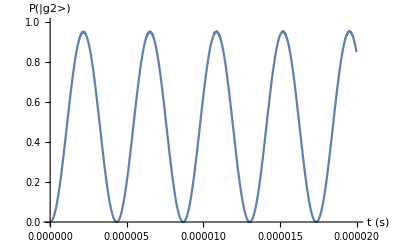

```mathematica
Ωr=2π 100*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=2(2π)/Ωr;
Δqb0=2π 50.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->Δqb0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

```mathematica
Ωr=2π 200*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=2(2π)/Ωr;
Δqb0=2π 450.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

## 3 level counter rotating

```mathematica
Clear[Δ]
```

```mathematica
Ha0=({{0, 0, 0}, {0, -ω0+Δqb, 0}, {0, 0, -ω0}});
Haf0=1/2({{0, Ω1 E^(I (ω0-Δ-Δqb+df) t)+Ω2 E^(I(ω0-Δ) t), Ω1 E^(I (ω0-Δ-Δqb+df) t)+Ω2 E^(I (ω0-Δ) t)}, {Ω1 E^(-I (ω0-Δ-Δqb+df) t)+Ω2 E^(-I (ω0-Δ) t), 0, 0}, {Ω1 E^(-I (ω0-Δ-Δqb+df) t)+Ω2 E^(-I (ω0-Δ) t), 0, 0}});
U=({{1, 0, 0}, {0, E^(I (ω0-Δ-Δqb+df) t), 0}, {0, 0, E^(I (ω0-Δ) t)}});
Ha=U.Ha0.U†;
MatrixForm[Ha];
Haf=U.Haf0.U†;
H=Ha+Haf-I D[U,t].U†;
FullSimplify[MatrixForm[H],Assumptions->{ω0∈Reals,t∈Reals,,Δ∈Reals,df∈Reals,Δqb∈Reals}]
```

(0 | 1/2 (Ω1+ⅇ^(-ⅈ t (df-Δqb)) Ω2) | 1/2 (ⅇ^(ⅈ t (df-Δqb)) Ω1+Ω2)
1/2 (Ω1+ⅇ^(ⅈ t (df-Δqb)) Ω2) | df-Δ | 0
1/2 (ⅇ^(-ⅈ t (df-Δqb)) Ω1+Ω2) | 0 | -Δ)

```mathematica
Hs=({{0, 1/2 (Ω1+ⅇ^(-ⅈ t (df-Δqb)) Ω2), 1/2 (ⅇ^(ⅈ t (df-Δqb)) Ω1+Ω2)}, {1/2 (Ω1+ⅇ^(ⅈ t (df-Δqb)) Ω2), df-Δ, 0}, {1/2 (ⅇ^(-ⅈ t (df-Δqb)) Ω1+Ω2), 0, -Δ}});
```

```mathematica
Ωr=2π 180.*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=10(2π)/Ωr;
Δqb0=2π 16.*10^3;
```

```mathematica
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->7];
```

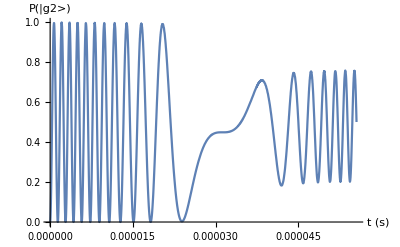

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"}]
```

```mathematica
Ωr=2π 180.*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=5(2π)/Ωr;
Δqb0=2π 16.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->Δqb0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->7];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0.95,1}]
```

-Graphics-

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

-Graphics-

```mathematica
Ωr=2π 1600.*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=4(2π)/Ωr;
Δqb0=2π 16.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

-Graphics-

```mathematica
Ωr=2π 180./4*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=4(2π)/Ωr;
Δqb0=2π 16.*10^3;
```

```mathematica
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->7];
```

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"}]
```

-Graphics-

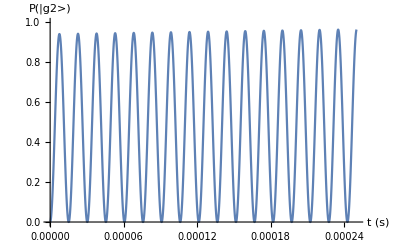

```mathematica
Ωr=2π 16*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=4(2π)/Ωr;
Δqb0=2π 16.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->Δqb0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

```mathematica
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

```mathematica
1/(4*0.01*10^-3)
```

25000.

25000.

```mathematica
Ωr=2π 100*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=2(2π)/Ωr;
Δqb0=2π 50.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->Δqb0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

-Graphics-

```mathematica
Ωr=2π 200*10^3;
Δ0=2π 240.*10^6;
Ω10=√(Ωr*(2*Δ0));
Ω20=√(Ωr*(2*Δ0));
Ttot=2(2π)/Ωr;
Δqb0=2π 450.*10^3;
Hn=Hs/.{Ω2->Ω20,Ω1->Ω10,Δ->Δ0,df->0,Δqb->Δqb0};
 ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,0,1}},ψ,{t,0,Ttot},AccuracyGoal->9];
Plot[Abs[Evaluate[ ψ[t] /.  ψs][[1,2]]]^2,{t,0,Ttot},AxesLabel->{"t (s)", "P(|g2>)"},PlotRange->{0,1}]
```

## light shift

```mathematica
Ωr=2π 25.*10^3;
Δ0=2π 240.*10^6;
Δ1=-2π 42.*10^6;
Δ2=-2π 14.*10^6;
Δ3=2π 16.*10^6;
Δ4=2π 48.*10^6;
Ω0=√(Ωr*(2*(Δ0)));
ωlf1=Ω0^2/(4(Δ0+Δ1));
ωlf2=Ω0^2/(4(Δ0+Δ3));
ωlf3=Ω0^2/(4(Δ0+Δ3));
ωlf4=Ω0^2/(4(Δ0+Δ4));
(ωlf1-ωlf4)/(2π)
```

4734.85

```mathematica
Ωr1=Ω0^2/(2(Δ0+Δ2));
Ωr2=Ω0^2/(2(Δ0+Δ3));
Ωr1/(2π)
Ωr2/(2π)
Ωr1/Ωr2
```

26548.7

23437.5

1.13274

## quantization axis

```mathematica
gl=1;
gs=2;
gj[s_,l_,j_]:= gl*(j*(j+1)-s*(s+1)+l*(l+1))/(2*j*(j+1))+gs*(j*(j+1)+s*(s+1)-l*(l+1))/(2*j*(j+1))
gf[i_,s_,l_,j_,f_]:=gj[s,l,j]*(f*(f+1)-i*(i+1)+j*(j+1))/(2*f*(f+1))
```

```mathematica
μN=5.050783699*10^-27;
μB=9.274009994*10^-24;
I0=(2*P0)/(π w0^2);
```

```mathematica
Fx=1/2({{0, √3, 0, 0}, {√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, √3, 0}});
Fy=1/(2 I)({{0, √3, 0, 0}, {-√3, 0, 2, 0}, {0, -2, 0, √3}, {0, 0, -√3, 0}});
Fz=({{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}});
Hb=μB/(2π ℏ)gf[1,1,1,3/2,1/2] (Bx Fx + By Fy + Bz Fz);
MatrixForm[Hb];
```

```mathematica
Itweezer=(2*P0)/(π w0^2);
He=1/4(10^-4)Itweezer*(αs IdentityMatrix[4]+αt ((Sin[θ]^2 Fy.Fy+Cos[θ]^2 Fz.Fz+Sin[θ]Cos[θ](Fy.Fz+Fz.Fy))-(Fx.Fx+Fy.Fy+Fz.Fz)));
H=Hb+He;
MatrixForm[Fy.Fz+Fz.Fy];
```

```mathematica
FullSimplify[He== He†, Assumptions->{θ∈Reals,αt∈Reals,αs∈Reals,P0∈Reals,w0∈Reals}]
```

True

```mathematica
Hn=H/.{Bx->0,By->0,Bz->0,θ->15.*π/180,αs->-22,αt->7.6,P0->0.006,w0->460.*10^-9};
Chop[Eigensystem[Hn]]
```

{{-2.19327×10^7,-2.19327×10^7,-1.50731×10^7,-1.50731×10^7},{{-0.159897-0.157078 ⅈ,-0.67691+0.689061 ⅈ,-0.0923167-0.0906888 ⅈ,0},{0,0.12941,0.-0.965926 ⅈ,0.224144},{-0.695217-0.682958 ⅈ,0.155687-0.158481 ⅈ,0.0212325+0.020858 ⅈ,0},{0,-0.0297637,0.+0.222159 ⅈ,0.974556}}}

```mathematica
Eigenvectors[Hn][[1]]
```

{-0.159897-0.157078 ⅈ,-0.67691+0.689061 ⅈ,-0.0923167-0.0906888 ⅈ,0.+0. ⅈ}

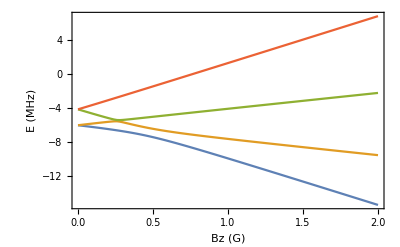

```mathematica
Bzs=Subdivide[0.,2*10^-4,100];
Hns=Table[H/.{Bx->0,By->0,Bz->Bzs[[i]],θ->π/10,αs->-22,αt->7.6,P0->0.006*0.9/3.3,w0->460.*10^-9},{i,1,Length[θs]}];
Es=Table[Sort[Eigenvalues[Hns[[i]]]],{i,1,Length[Hns]}];
EsB=Table[{Bzs*10^4,Transpose[Es][[i]]/10^6},{i,1,4}];
EsBT=Table[Transpose[EsB[[i]]],{i,1,4}];
ListPlot[{EsBT[[1]],EsBT[[2]],EsBT[[3]],EsBT[[4]]},Joined->True,Frame->True,FrameLabel->{"Bz (G)", "E (MHz)"}]
```

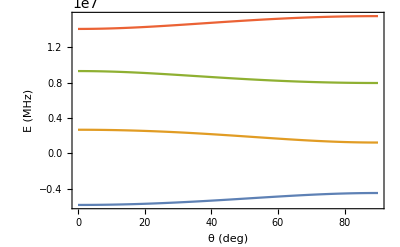

```mathematica
θs=Subdivide[0.,π/2.,100];
Hns=Table[H/.{Bx->0,By->0,Bz->1.8*10^-4,θ->θs[[i]],αs->-22,αt->7.6,P0->0.006*0.9/3.3,w0->460.*10^-9},{i,1,Length[θs]}];
Es=Table[Sort[Eigenvalues[Hns[[i]]]],{i,1,Length[Hns]}];
EsB=Table[{θs*180/π,Transpose[Es][[i]]},{i,1,4}];
EsBT=Table[Transpose[EsB[[i]]],{i,1,4}];
ListPlot[{EsBT[[1]],EsBT[[2]],EsBT[[3]],EsBT[[4]]},Joined->True,Frame->True,FrameLabel->{"θ (deg)", "E (MHz)"}]
```

```mathematica
Hn=H/.{Bx->0,By->0,Bz->1.8*10^-4,θ->π/2,αs->-22,αt->7.6,P0->0.006*0.9/3.3,w0->460.*10^-9}
```

{{1.5477×10^7,0.+0. ⅈ,810081.,0.},{0.+0. ⅈ,7.89955×10^6,0.,810081.},{810081.,0.,1.25753×10^6,0.+0. ⅈ},{0.,810081.,0.+0. ⅈ,-4.44909×10^6}}